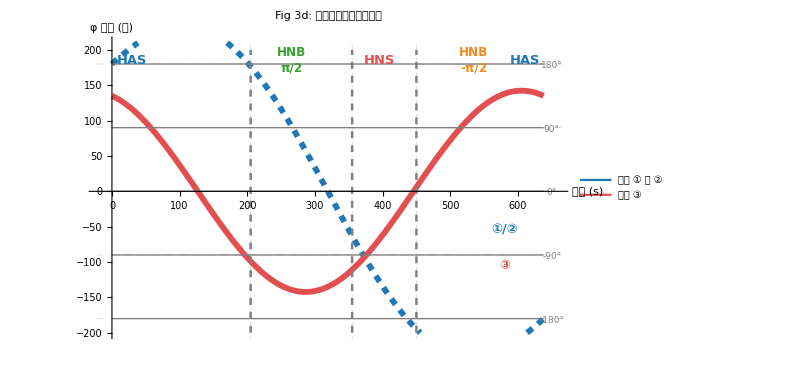

```mathematica
(* =========================================*)(*Fig 3d:胶体取向角的时间演化*)ClearAll["Global`*"]

phi12Smooth[t_]:=180*Cos[Pi*t/638]+90*Sin[Pi*t/319]//N
phi3Smooth[t_]:=135*Cos[Pi*t/319]-45*Sin[Pi*t/319]//N

Plot[{phi12Smooth[t],phi3Smooth[t]},{t,0,638},PlotStyle->{{RGBColor[0.12,0.47,0.71],Thickness[0.007],Dashed},{RGBColor[0.89,0.31,0.31],Thickness[0.007]}},PlotRange->{{-20,660},{-200,210}},AxesLabel->{Style["时间 (s)",14],Style["φ 角度 (度)",14]},PlotLabel->Style["Fig 3d: 胶体取向角的时间演化",16,Bold],GridLines->{{205,355,450},{-180,-90,0,90,180}},GridLinesStyle->Directive[Gray,Dashed,Opacity[0.4]],ImageSize->600,PlotLegends->Placed[LineLegend[{RGBColor[0.12,0.47,0.71],RGBColor[0.89,0.31,0.31]},{"胶体 ① 和 ②","胶体 ③"},LegendFunction->"Frame"],{0.85,0.85}],Epilog->{Text[Style["HAS",RGBColor[0.12,0.47,0.71],13,Bold],{30,185}],Text[Style["HNB\nπ/2",RGBColor[0.20,0.63,0.17],12,Bold],{265,185}],Text[Style["HNS",RGBColor[0.89,0.31,0.31],13,Bold],{395,185}],Text[Style["HNB\n-π/2",RGBColor[0.95,0.55,0.10],12,Bold],{535,185}],Text[Style["HAS",RGBColor[0.12,0.47,0.71],13,Bold],{610,185}],{RGBColor[0.12,0.47,0.71],Text[Style["①/②",13,Bold],{580,-55}]},{RGBColor[0.89,0.31,0.31],Text[Style["③",13,Bold],{580,-105}]},{Gray,Dashed,Thickness[0.003],Line[{{205,-200},{205,200}}]},{Gray,Dashed,Thickness[0.003],Line[{{355,-200},{355,200}}]},{Gray,Dashed,Thickness[0.003],Line[{{450,-200},{450,200}}]},{Gray,Thin,Line[{{0,180},{638,180}}]},{Gray,Thin,Line[{{0,90},{638,90}}]},{Gray,Thin,Line[{{0,0},{638,0}}]},{Gray,Thin,Line[{{0,-90},{638,-90}}]},{Gray,Thin,Line[{{0,-180},{638,-180}}]},Text[Style["180°",9,Gray],{650,178}],Text[Style["90°",9,Gray],{650,88}],Text[Style["0°",9,Gray],{650,-2}],Text[Style["-90°",9,Gray],{650,-92}],Text[Style["-180°",9,Gray],{650,-182}]}]
```